```mathematica
NMinimize[2 Cos[a]+2 Cos[a+b]+1 Sin[a]+1 Sin[a+b],{a}]
```

NMinimize::nnum: The function value 0.613858  + 2\ Cos[0.829053  - b] - Sin[0.829053  - b] is not a number at {a} = {-0.829053}.

General::stop: Further output of NMinimize :: nnum will be suppressed during this calculation.

NMinimize[2 Cos[a]+2 Cos[a+b]+Sin[a]+Sin[a+b],{a}]

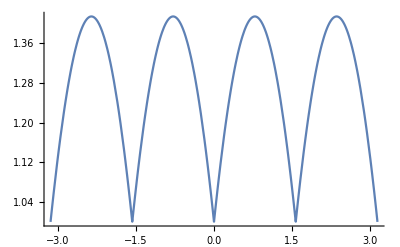

```mathematica
Plot[Abs[Cos[t]]+Abs[Sin[t]],{t,-π,π}]
```

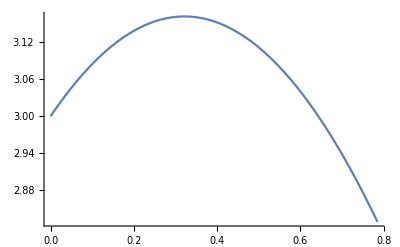

```mathematica
Plot[2Cos[a]+2Sin[a]+Cos[a+π/2]+Sin[a+π/2],{a,0,π/4}]
```

```mathematica
TrigExpand[c1 Cos[a]+c1 Sin[a] + c2 Cos[a+b] + c2 Sin[a+b]]
```

c1 Cos[a]+c2 Cos[a] Cos[b]+c1 Sin[a]+c2 Cos[b] Sin[a]+c2 Cos[a] Sin[b]-c2 Sin[a] Sin[b]

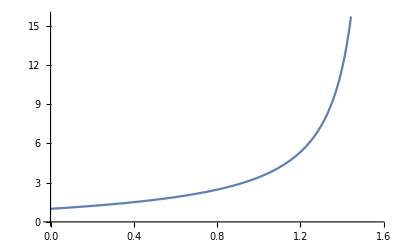

```mathematica
c2=1;
c1=1;
F[β_]=(c2+c1 Sin[β]+c1 Cos[β])/(c2+c1 Cos[β]-c1 Sin[β]);
Plot[F[x],{x,0,π/2}]
```

```mathematica
c1=1;
c2=1;
c3=1;
c4=1;
β=π/6;
γ=π/3;
δ=π/2;
F[α_]=c1 Cos[α]+c1 Sin[α]+c2 Cos[α+β]+c2 Sin[α+β]+c3 Cos[α+β+γ]+c3 Sin[α+β+γ]+c4 Cos[α+β+γ+δ]+c4 Sin[α+β+γ+δ]
Plot[F[α],{α,0,π/4}]
```

Cos[α]+Cos[π/6+α]-Sin[α]+Sin[π/6+α]

```mathematica
Minimize[Cos[α]+Cos[π/6+α]-Sin[α]+Sin[π/6+α],{α}]
```

{Cos[2 ArcTan[(2 √6)/(3-√3)+(-3-√3)/(-3+√3)]]+Cos[π/6+2 ArcTan[(2 √6)/(3-√3)+(-3-√3)/(-3+√3)]]-Sin[2 ArcTan[(2 √6)/(3-√3)+(-3-√3)/(-3+√3)]]+Sin[π/6+2 ArcTan[(2 √6)/(3-√3)+(-3-√3)/(-3+√3)]],{α→2 ArcTan[(2 √6)/(3-√3)+(-3-√3)/(-3+√3)]}}

```mathematica
Simplify[%82]
```

c1 Cos[α]+c2 Cos[α+β]+c3 Cos[α+β+γ]+c1 Sin[α]+c2 Sin[α+β]+c3 Sin[α+β+γ]

c1 Cos[α]+c2 Cos[α] Cos[β]+c3 Cos[α] Cos[β] Cos[γ]-c1 Sin[α]-c2 Cos[β] Sin[α]-c3 Cos[β] Cos[γ] Sin[α]-c2 Cos[α] Sin[β]-c3 Cos[α] Cos[γ] Sin[β]-c2 Sin[α] Sin[β]-c3 Cos[γ] Sin[α] Sin[β]-c3 Cos[α] Cos[β] Sin[γ]-c3 Cos[β] Sin[α] Sin[γ]-c3 Cos[α] Sin[β] Sin[γ]+c3 Sin[α] Sin[β] Sin[γ]

```mathematica
c1 Cos[α]+c2 Cos[α] Cos[β]+c3 Cos[α] Cos[β] Cos[γ]+c1 Sin[α]+c2 Cos[β] Sin[α]+c3 Cos[β] Cos[γ] Sin[α]+c2 Cos[α] Sin[β]+c3 Cos[α] Cos[γ] Sin[β]-c2 Sin[α] Sin[β]-c3 Cos[γ] Sin[α] Sin[β]+c3 Cos[α] Cos[β] Sin[γ]-c3 Cos[β] Sin[α] Sin[γ]-c3 Cos[α] Sin[β] Sin[γ]-c3 Sin[α] Sin[β] Sin[γ]
```

c1 Cos[α]+c2 Cos[α] Cos[β]+c3 Cos[α] Cos[β] Cos[γ]+c1 Sin[α]+c2 Cos[β] Sin[α]+c3 Cos[β] Cos[γ] Sin[α]+c2 Cos[α] Sin[β]+c3 Cos[α] Cos[γ] Sin[β]-c2 Sin[α] Sin[β]-c3 Cos[γ] Sin[α] Sin[β]+c3 Cos[α] Cos[β] Sin[γ]-c3 Cos[β] Sin[α] Sin[γ]-c3 Cos[α] Sin[β] Sin[γ]-c3 Sin[α] Sin[β] Sin[γ]

```mathematica
Simplify[%60]
```

c1 Cos[α]+c2 Cos[α+β]+c3 Cos[α+β+γ]+c1 Sin[α]+c2 Sin[α+β]+c3 Sin[α+β+γ]

```mathematica
∂_c1 %
```

0

```mathematica
TrigReduce[%60]
```

c1 Cos[α]+c2 Cos[α+β]+c3 Cos[α+β+γ]+c1 Sin[α]+c2 Sin[α+β]+c3 Sin[α+β+γ]

```mathematica
Clear[c1,c2,c3];
Collect[TrigExpand[c1 Cos[α]+c1 Sin[α]+c2 Cos[α+β]+c2 Sin[α+β]+c3 Cos[α+β+γ]+c3 Sin[α+β+γ]],{Sin[α],Cos[α]}]
```

```mathematica
ϕ
```

```mathematica
Plot3D[Abs[Cos[θ]]+Abs[Sin[θ]Sin[ϕ]]+Abs[Sin[θ]Cos[ϕ]],{θ,0,π},{ϕ,0,2*π}]
```

-Graphics3D-